```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

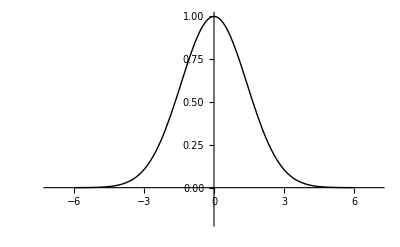
{cos(t ω) -Graphics-_0-m ω sin(t ω) x_0,cos(t ω) x_0+(sin(t ω) -Graphics-_0)/(m ω)}

```mathematica
Clear[energy, radiusInNonDimensionalizedCoordinates, theta, phasePoint]

(* passing points in phase space (p, x) = {., .} *)

energy[m_, ω_, p0_] :=(p0[[1]])^2/(2m) + m ω^2 (p0[[2]])^2/2 ;
radiusInNonDimensionalizedCoordinates[m_, ω_, p0_] := Sqrt[2 energy[m, ω, p0]/m] ;

theta[m_, ω_, p0_] :=ArcTan[ ω m p0[[2]]/p0[[1]]] ; (* x/p *)

phasePoint[t_, m_, ω_, p0_] := 
radiusInNonDimensionalizedCoordinates[m, ω, p0]{
m    Cos[ ω t + theta[m, ω, p0] ] ,
(1/ω)  Sin[ ω t + theta[m, ω, p0] ] 
} ;


FullSimplify[  TrigExpand[  phasePoint[t, m, ω, {Subscript[p, 0], Subscript[x, 0]}] ],Subscript[p, 0]> 0 && Subscript[x, 0] > 0 && m > 0 &&  ω > 0] // TraditionalForm

 
Manipulate[
DynamicModule[{ differenceOfPoints, averagePositionBetweenPoints, radiusOfCircleAtAveragePos, c},

differenceOfPoints = plOuter - plInner ; 
averagePositionBetweenPoints = (plOuter  + plInner)/2 ;
radiusOfCircleAtAveragePos = 0.8 Norm[differenceOfPoints]/2 ;
c[v_] = averagePositionBetweenPoints + radiusOfCircleAtAveragePos {Cos[v], Sin[v]} ;

Show[{
ParametricPlot[
{
phasePoint[u 2 Pi/ω, m, ω, plInner],
phasePoint[u 2 Pi/ω, m, ω, plOuter],
c[2 Pi u],
phasePoint[t1, m, ω, c[2 Pi u]],
phasePoint[t2, m, ω, c[2 Pi u]],
phasePoint[t3, m, ω, c[2 Pi u]]
},
{u,0,1},
 PlotRange -> 4,
PlotStyle->Thick,
AxesLabel->{p, x}
 ] (* plot *)
,
Graphics[{
Text["(p_(0,)x_0)", {plInner[[1]] + 0.4,plInner[[2]] + 0.4}],
Text["(p_(1,)x_1)", {plOuter[[1]] + 0.4,plOuter[[2]] + 0.4}]
}]
} ] (* show *)

]
,
{{t1, 5.5}, 0, 20},
{{t2, 8.65}, 0, 20},
{{t3, 6.65}, 0, 20},
{{m,1}, 0.1, 10},
{{ω , Pi/2}, Pi/10, 10 Pi},
{{plInner,{1,1}},Locator},
{{plOuter,{2,2}},Locator}

] (* manip *)
```

```mathematica
shoPhaseSpacePlotsFig1 = DynamicModule[{m=1,plInner={1,1},plOuter={2,2},t1=5.5,t2=8.65,t3=6.65,ω=π/2},DynamicModule[{differenceOfPoints,averagePositionBetweenPoints,radiusOfCircleAtAveragePos,c},differenceOfPoints=plOuter-plInner;averagePositionBetweenPoints=(plOuter+plInner)/2;radiusOfCircleAtAveragePos=1/2 0.8 Norm[differenceOfPoints];c[v_]=averagePositionBetweenPoints+radiusOfCircleAtAveragePos {Cos[v],Sin[v]};Show[{ParametricPlot[{phasePoint[(u 2 π)/ω,m,ω,plInner],phasePoint[(u 2 π)/ω,m,ω,plOuter],c[2 π u],phasePoint[t1,m,ω,c[2 π u]],phasePoint[t2,m,ω,c[2 π u]],phasePoint[t3,m,ω,c[2 π u]]},{u,0,1},PlotRange->4,PlotStyle->Thick,AxesLabel->{p,x}],Graphics[{Text["(\!\(\*SubscriptBox[\(p\), \(\(0\)\(,\)\)]\)\!\(\*SubscriptBox[\(x\), \(0\)]\))",{plInner⟦1⟧+0.4,plInner⟦2⟧+0.4}],Text["(\!\(\*SubscriptBox[\(p\), \(\(1\)\(,\)\)]\)\!\(\*SubscriptBox[\(x\), \(1\)]\))",{plOuter⟦1⟧+0.4,plOuter⟦2⟧+0.4}]}]}]]]
```

```mathematica
DynamicModule[{m=1,pl={0.96,2.5200000000000005},ω=1.4338228870983816},

Module[
{th$},th$=theta[m,ω,pl];
Show[
{
ParametricPlot[
phasePoint[t,m,ω,pl],
{t,0,20},
PlotRange->4,
PlotStyle->Thick,
AxesLabel->{p, x}
],
Graphics[{
PointSize[Large](*, Pink*),Point[pl],
Text["(p_(0,)x_0)", {pl[[1]] + 0.3,pl[[2]] + 0.3}]
}]
}
]
]
]
```

```mathematica
pendulumPhaseSpaceFig2 = DynamicModule[{m=1,pl={0.96,2.5200000000000005},ω=1.4338228870983816},
Module[
{th$},th$=theta[m,ω,pl];

ParametricPlot[
phasePoint[t,m,ω,pl],
{t,0,20},
PlotRange->4,
PlotStyle->{Thick,Black},
Ticks -> None,
AxesLabel->{ 
(*Row[{1/(l "ω"),Sqrt[ Row[{2, "E"}]/"m"]}] //fs, 
l Sqrt[Row[{2, "m E"}] ] // fs *)
MaTeX["\\frac{1}{l \\omega} \\sqrt{ \\frac{2 E}{m}}"],
MaTeX["l \\sqrt{ 2 m E }"]
}
]
]
]
```

```mathematica
peeters`exportForLatex["pendulumPhaseSpaceFig2",pendulumPhaseSpaceFig2]
```

{pendulumPhaseSpaceFig2.eps,pendulumPhaseSpaceFig2pn.png}

```mathematica
peeters`exportForLatex["shoPhaseSpacePlotsFig1",shoPhaseSpacePlotsFig1]
```

{shoPhaseSpacePlotsFig1.eps,shoPhaseSpacePlotsFig1pn.png}

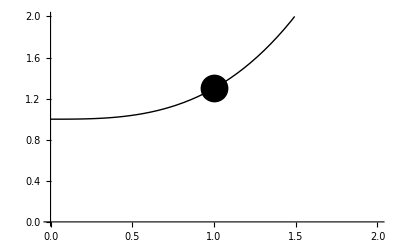

```mathematica
ClearAll[f]
f[x_] := 0.3 x^3 + 1
lecture8Fig7 = Show[{
Plot[f[x], {x,0, 2},
PlotRange-> {{0,2}, {0, 2}},
PlotStyle-> {Thick, Black},
AxesLabel-> {
MaTeX["x"],
MaTeX["E"]
},
Ticks -> None
]
, Graphics[{
Black,
PointSize -> 0.05,
Point[ {1, f[1]} ]
}]}]
```

```mathematica
peeters`exportForLatex["lecture8Fig7",lecture8Fig7]
```

{lecture8Fig7.eps,lecture8Fig7pn.png}

```mathematica
(*Plot[Sinh[1/t], {t, 0, 1}]*)
```